## Sequências e séries

### Definição

## PA

a_n=a_(n-1)+d.

Variáveis: a_1 e d.

```mathematica
Table[Nest[Function[{a},a+d],1,n],{n,0,10}]
```

{1,1+d,1+2 d,1+3 d,1+4 d,1+5 d,1+6 d,1+7 d,1+8 d,1+9 d,1+10 d}

```mathematica
Clear[PA];
(*Esta função é um table que retorna sequências para valores de d*)
PA=Function[{a0,d},
	Table[Nest[
		Function[{a},a+d],a0,n],{n,0,10}
	]
];
```

```mathematica
PA[1,1]
```

{1,2,3,4,5,6,7,8,9,10,11}

```mathematica
PA[1,2]
```

{1,3,5,7,9,11,13,15,17,19,21}

```mathematica
PA[2,2]
```

{2,4,6,8,10,12,14,16,18,20,22}

Assumindo x∈ℕ.

P.A.s a+x com a=-75, -20≤x≤30:

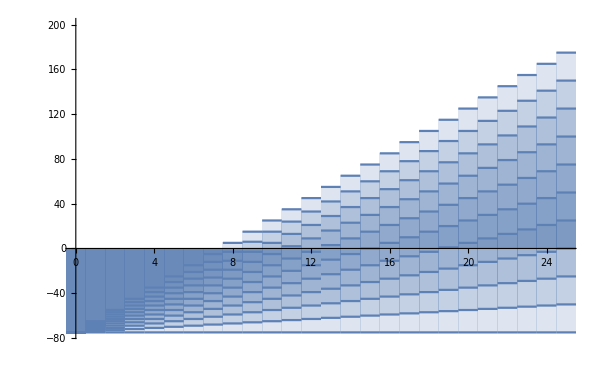

```mathematica
DiscretePlot[PA[-75,d],{d,-25,25},ExtentSize->Full,PlotRange->{-75,200},RegionFunction->Function[{x,y},x≥0],ImageSize->600]
```

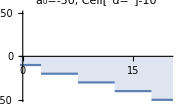
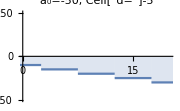
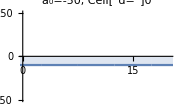
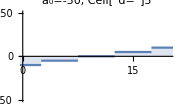
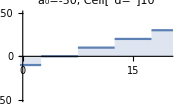
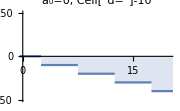
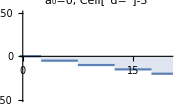
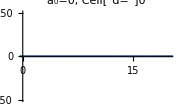

```mathematica
Column@Table[Row@Table[DiscretePlot[a0+x d,{x,-20,20,5},ExtentSize->Full,RegionFunction->Function[{x,y},x≥0],ImageSize->180,PlotRange->{-250,250},PlotLabel->StringForm["a_0=``, Cell["d=",ExpressionUUID->"1fe792fb-7e91-4aa1-aaa5-26a4f6cb3192"]``",a0,d]],{d,-10,10,5}],{a0,-50,50,50}]
```

## PG

Cada termo (b) é o anterior ×q.

b_n=b_(n-1)·q.

Variáveis: b_1 e q.

PAs apenas são constantes ou não dependendo de se d=0.

```mathematica
Clear[PG];
(*Esta função é um table que retorna sequências para valores de d*)
PG=Function[{b0,q},
	Table[Nest[
		Function[{b},b*q],b0,n],{n,0,10}
	]
];
```

```mathematica
PG[1,2]
```

{1,2,4,8,16,32,64,128,256,512,1024}

```mathematica
PG[1,3]
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

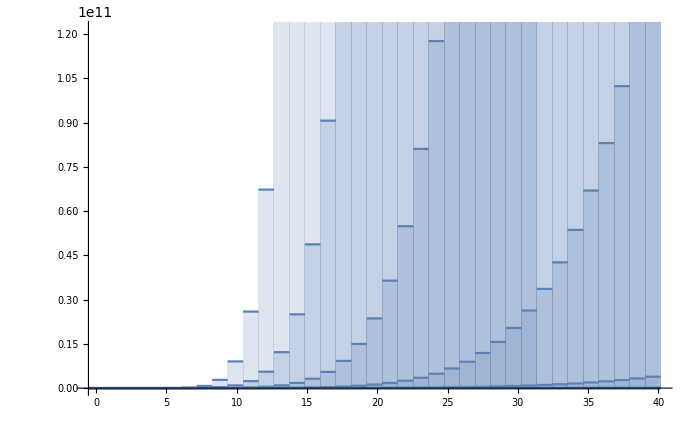

```mathematica
DiscretePlot[PG[1,q],{q,0,40,1.1},ExtentSize->Full,RegionFunction->Function[{x,y},x≥0],ImageSize->700]
```

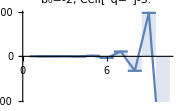
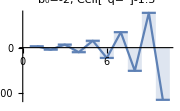
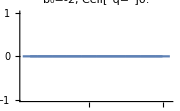
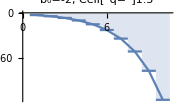
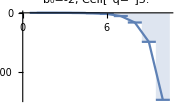
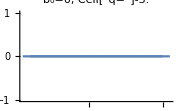
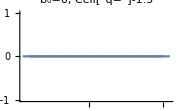
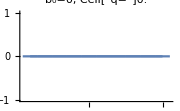

```mathematica
Column@Table[Row@Table[DiscretePlot[Nest[Function[{b},b*q],b0,n],{n,1,10},ExtentSize->Full,Joined->True,ImageSize->180,(*PlotRange->{-125,125},*)PlotLabel->StringForm["b_0=``, Cell["q=",ExpressionUUID->"fe02af02-9428-4727-aa53-ece997d90d90"]``",b0,q]],{q,-3,3,1.5}],{b0,-2,2,2}]
```

PGs com q negativo não “convergem” (“divergem”) (porque o sinal está sempre trocando porque o multiplicador é negativo);

PGs com q=0 são constantes exceto o primeiro termo;

PGs com q=1 são constantes;

PGs com 0<q<1 "convergem" para 0;

PGs com q>0 "convergem" para ±∞ dependendo do sinal de b_0.

```mathematica
Manipulate[
	DiscretePlot[Nest[Function[{b},b*q],b0,n],{n,1,10},ExtentSize->Full,Joined->True,ImageSize->350,PlotRange->{-10,10},
	PlotLabel->StringForm["b_0=``, Cell["q=",ExpressionUUID->"2bb72c01-3970-433f-b5d9-d7a866821ec2"]``",b0,q]],{{b0,-3.5},-7.5,7.5,.1},{{q,.8},-2,2,.1}
]
```

### Fórmulas

PA termo. a_n=a_1+d(n-1).

Porquê n-1? Porque supomos n indexado em 1. E o primeiro termo não tem diferença para a_1. Se usarmos indexado em 0, a_n=a_0+d n, ou seja, é só uma reparação sobre a fórmula trivial.

PG termo. b_n=b_(n-1)·q. Isso é a fórmula dado um termo b_(n-1), não a geral. Na geral, o termo inicial é multiplicado por q n-1 vezes. A quantidade de vezes que um número é multiplicado por si mesmo é o número elevado à quantidade: 2·2·2·2=2^4. Agora se um número a é multiplicado por outro b n vezes... a·b·b·b·b=a·b^4=a·b^n. Então temos o valor do termo n como b_1·q^n? Novamente, se indexado em 1, o n-ésimo termo tem uma multiplicação a menos, pois o primeiro termo não é multiplicado. Então b_n=b_1·q^(n-1). (Se fosse indexado em 0, seria b_0·q^n, ou seja, o mesmo que a fórmula da PA porém multiplicando o primeiro termo ao invés de somando e exponenciada a razão ao invés de multiplicada.)

PA soma dos n primeiros termos. S_n=a_1+a_2+...+a_n=((a_1+a_n)·n)/2. Demonstração não trivial.

PG soma dos n primeiros termos. S_n=b_1·(1-q^n)/(1-q) (com q≠1). Entender a fórmula. Demonstrada na aula 02.

Segundo [2], se |q|<1, a soma geral da PG (1-q^(n+1))/(1-q) tem limite (ou é igual a?) 1/(1-q) é b_1/(1-q) (isto está na aula 00).

### Parâmetros

#### Progressão aritmética

(n)→a n+c, com 1≤n≤10

```mathematica
Manipulate[
Module[{seq},
seq=Function[{n},a n +c];
DiscretePlot[seq[n],{n,1,10},ExtentSize->Full,ImageSize->350,PlotRange->{0,1000}]
],
{{a,1},0,100,1},
{{c,0},0,1000,1}
]
```

#### Progressão geométrica

(n)→a b^n, com 1≤n≤10

```mathematica
Manipulate[
Module[{seq},
seq=Function[{n},a b^n];
DiscretePlot[seq[n],{n,1,10},ExtentSize->Full,ImageSize->350,PlotRange->{0,1000}]
],
{{a,1},0,10,1},
{{b,1},0,3,.1}
]
```

### Provas

Fórmula do termo da PA. Por indução.

Primeiro, para k=1: a_1=a_1+d(1-1)=a_1□.

Sendo válido para n=k, provar para n=k+1.

a_(k+1)=a_1+d(k+1-1)=a_1+d k.
Agora, a_n=a_(n-1)+d sempre. Então a_(k+1)=a_(k+1-1)+d=a_k+d.
Logo, a_k+d=a_1+d k. (?)
a_1+d k=a_(k+1)=a_k+d.

De novo.

Para k=1, a_1=a_1+d 0 =a_1□.
Para k+1, a_(k+1)=a_1+d k.
a_k=a_1+d(k-1).
a_1+d(k-1)-a_1-d k=d(k-1-k)=d. Mas isso prova? Sim, pois esta é a definição de PA.
Temos que provar que a_(k+1)=a_k+d.
a_1+d k=a_1+d(k-1)+d⇒
d k=(d k)-d+d□.

Fórmula da soma da PA, por indução.

S_n=((a_1+a_n)·n)/2.

Para o caso n=k=1, 
S_1=((a_1+a_1)·1)/2=(2 a_1)/2=a_1.

Para n=k+1, 
S_(k+1)=((a_1+a_(k+1))·(k+1))/2. Como S_n=S_(n-1)+d errado. S_n=S_(n-1)+n.
S_(k+1)=S_k+d=((a_1+a_k)·n)/2+d. Logo, 
((a_1+a_(k+1))·n)/2=((a_1+a_k)·n)/2+d⇒
(a_1+a_(k+1))·n=(a_1+a_k)·n+2d⇒
n a_1+n a_(k+1)=n a_1+n a_k+2d⇒
n a_(k+1)=n a_k+2d⇒
n a_k+d=n a_k+d+d.

Estamos tentando provar que? S_(n+1)-S_n=d? Neste caso,

((a_1+a_(n+1))·n)/2-((a_1+a_n)·n)/2=d⇒
n(a_1+a_n+d+a_1+a_n)=2d⇒
n(2 a_1+2 a_n+d)=2d⇒?

Provar que S_(n+1)-S_n=n. Errado. S_n-S_(n-1)=n. Porém, S_(n+1)-S_n=n+1.

((a_1+a_(k+1))·(k+1))/2-((a_1+a_k)·k)/2=k+1⇒
(a_1+a_(k+1))·(k+1)-(a_1+a_k)·k=2k+2.

Expressar a_(k+1) em termos de a_k.

(a_1+a_k+d)·(k+1)-(a_1 k+a_k k)=2k+2⇒
a_1 k+a_1+a_k k+a_k+d k+d-a_1 k-a_k k=2k+2⇒
a_1+a_k+d k+d=2k+2.

a_(k+1)=a_1+k d⇒a_k=a_1+(k-1)d.

a_1+a_1+(k-1)d+d k+d=2k+2⇒
2 a_1+d(k-1+k+1)=2k+2⇒
2 a_1+2d k=2k+2⇒
a_1+d k=k+1.

Como a_1+d k=a_(k+1),

a_(k+1)=k+1?

De novo. Seguindo [1], a fórmula para n=k+1 é apenas a fórmula para n=k acrescida do último termo, a_(k+1).

(1) S_(k+1)=((a_1+a_k)·k)/2+a_(k+1).

Temos algumas substituições.

a_n=a_(n-1)+d.
a_n=a_(n+1)-d.
a_(n+1)=a_n+d.
a_(n-1)=a_n-d.
S_n=S_(n-1)+n.
S_n=S_(n+1)-n.
S_(n+1)=S_n+n+1.
S_(n-1)=S_n-(n+1).
a_n=a_1+(n-1)d.
a_(n+1)=a_1+n d.
a_(n-1)=a_1+(n-1)d.

As “trocas de variável” envolvem trocar a_n por a_(n±x) ou S_n por S_(n±x) ou a_n por a_1±x.

Substituindo dois desses em (1),

S_(k+1)=((a_1+a_1+(k-1)d)·k)/2+a_1+k d.

Fizemos duas trocas de a_k por a_1+x.

S_(k+1)=(2 a_1+k d-d)k+2 a_1+2k d=
2 a_1 k+k^2 d-k d+2 a_1+2 k d=
k(2 a_1+k d-d+2d)+2 a_1=
k(2 a_1+k d+d)+2 a_1.

De novo.

Estamos tentando provar que S_(k+1)=((a_1+a_(k+1))·(k+1))/2.
Primeira substituição a_k por a_(k+1)-d.

S_(k+1)=((a_1+a_(k+1)-d)k)/2+a_(k+1).

Segunda substituição de a_(k+1) por a_1+k d.

Basicamente, as minhas substituições foram ao contrário.

S_(k+1)=((a_1+a_(k+1)-d)k)/2+a_1+k d=
(a_1 k+a_(k+1)k-d k+a_1+k d)/2=
(k(a_1+a_(k+1)-d+d)+a_1)/2=
(k(a_1+a_(k+1))+a_1)/2.

Substituindo a_(k+1) por a_1+k d, (porquê?)

(k(a_1+a_1+k d)+a_1)/2=
(k(2 a_1+k d)+a_1)/2.

((a_1+a_(k+1))·(k+1))/2=(k(2 a_1+k d)+a_1)/2?
(a_1+a_(k+1))·(k+1)=k(2 a_1+k d)+a_1?

Voltando a antes desta última substituição.

((a_1+a_(k+1))·(k+1))/2=(k(a_1+a_(k+1))+a_1)/2?
(a_1+a_(k+1))·(k+1)=k(a_1+a_(k+1))+a_1?
a_1k+a_(k+1)k+a_1+a_(k+1)=a_1 k+a_(k+1)k+a_1? Não.

Prova desenvolvida no papel.

Fórmula do termo da PG, por indução.

Fórmula da soma da PG, por indução.

Fórmula da soma da PG, pela demonstração de Gauss.

Minha fórmula PG termo com base em termo arbitrário.
b_(m+n)=b_n q^m=b_m q^n.
b_(m-n)=b_n q^-m=b_m q^-n.

### Exercícios

```mathematica
{(-1/2)^6,16/189,Module[{q},q=-1/2;(1-q^6)/(1-q)]}
```

{1/64,16/189,21/32}

```mathematica
Column@{"0,0"->PG[0,0],"-1,0"->PG[-1,0],"-1,-.1"->PG[-1,-.1],"0,-.1"->PG[0,-.1],"0,.1"->PG[0,.1],"1,-.1"->PG[1,-.1],"1,0"->PG[1,0],"1,.1"->PG[1,.1],"1,1"->PG[1,1],"2,1"->PG[2,1]}
```

0,0→{0,0,0,0,0,0,0,0,0,0,0}
-1,0→{-1,0,0,0,0,0,0,0,0,0,0}
-1,-.1→{-1,0.1,-0.01,0.001,-0.0001,0.00001,-1.×10^-6,1.×10^-7,-1.×10^-8,1.×10^-9,-1.×10^-10}
0,-.1→{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
0,.1→{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
1,-.1→{1,-0.1,0.01,-0.001,0.0001,-0.00001,1.×10^-6,-1.×10^-7,1.×10^-8,-1.×10^-9,1.×10^-10}
1,0→{1,0,0,0,0,0,0,0,0,0,0}
1,.1→{1,0.1,0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}
1,1→{1,1,1,1,1,1,1,1,1,1,1}
2,1→{2,2,2,2,2,2,2,2,2,2,2}

```mathematica
Module[{pg},pg=PG[2,2];{pg,{pg[[4]],pg[[2]]*2^2},{pg[[8]],pg[[5]]*2^3},{pg[[8]],pg[[3]]*2^5},{pg[[5]],pg[[8]]*2^-3}}]
```

{{2,4,8,16,32,64,128,256,512,1024,2048},{16,16},{256,256},{256,256},{32,32}}

```mathematica
{2^-2,√2,1/2^2,42/3,49*4}
```

{1/4,√2,1/4,14,196}

```mathematica
{√324,2^13,4/-1,Sum[2^x,{x,0,12}],(1-2^13)/(1-2),2^6,8191/63,(1-2^6)/(1-2),Sum[2^x,{x,0,12}]/Sum[2^x,{x,0,5}]}
```

{18,8192,-4,8191,8191,64,8191/63,63,8191/63}

```mathematica
{1.34-1.33,1.344-1.333,1.3444-1.3333,1.344444-1.333333,(.1)^2,(.1)^3,(.1)^2+(.1)^3,Sum[(.1)^n,{n,2,2}],Sum[(.1)^n,{n,2,3}],1/3+Sum[(.1)^n,{n,2,10}],1/3+Sum[(.1)^n,{n,0,10}],1/3+Sum[(.1)^n,{n,0,10}]-(.1)^1,1/3-1/10,7/30+Sum[(.1)^n,{n,0,10}],363/270,7/30+1/(1-1/10)}
```

{0.01,0.011,0.0111,0.011111,0.01,0.001,0.011,0.01,0.011,0.344444,1.44444,1.34444,7/30,1.34444,121/90,121/90}

```mathematica
{1/6^7,(1/6)^7,N@6/5,√72,Simplify[a^2+a^3],(7/3)^3+7/3,Simplify[(1-a^3)/(1-a^2)],7/30+1/(1-1/10)}
```

{1/279936,1/279936,1.2,6 √2,a^2 (1+a),406/27,(1+a+a^2)/(1+a),121/90}

```mathematica
{Simplify[a(1+q^3)*a^2 q^3],14-336+14+336+14,√336,14-√336+14+14+√336,42/3,√98}
```

{a^3 q^3 (1+q^3),42,4 √21,42,14,7 √2}

```mathematica
{a^3 q^3 (1+q^3),42,4 √21,42,14,7 √2,7-√98+7+7 √98,√98,14^2,14^4,2^14,16383/127,121*180/90,19^2,√(361-28),√72,Roots[d^2-10d+7==0,d]}
```

{a^3 q^3 (1+q^3),42,4 √21,42,14,7 √2,14+42 √2,7 √2,196,38416,16384,129,242,361,3 √37,6 √2,d==5-3 √2||d==5+3 √2}

```mathematica
{(10-(10+√72)/2)*7+49/((10+√72)/2),((10±√72)/2)*7,(119+7 √72)/2,N@((119+7 √72)/2),56*((10±√72)/2),N[56*((10±√72)/2)],Simplify[a^3 q^3+a^3 q^6],(a^3 q^3+a^3 q^6)/(a q^3),(49/((10±√72)/2))+(7*((10±√72)/2)),Roots[q^4-3 q^2==10,q],Roots[q^2-3q==10,q]}
```

{98/(10+6 √2)+7 (10+1/2 (-10-6 √2)),7/2 (10±6 √2),1/2 (119+42 √2),89.1985,28 (10±6 √2),28. (10.±8.48528),a^3 q^3 (1+q^3),(a^3 q^3+a^3 q^6)/(a q^3),98/(10±6 √2)+7/2 (10±6 √2),q==ⅈ √2||q==-ⅈ √2||q==√5||q==-√5,q==-2||q==5}

### Referências

[1] https://www.purplemath.com/modules/series6.htm

[2] https://math.stackexchange.com/a/2495425/479728